```mathematica
data={{29.2,3040},{30.7,3840},{24.7,2470},{32.3,3610},{31.3,3480},{31.5,3810},{24.5,2330},{19.9,1800},{27.3,3110},{27.1,3160},{24,2310},{33.8,4360},{21.5,1880},{32.2,3670},{22.5,1740},{27.5,2250},{25.6,2650},{34.5,4970},{26.2,2620},{26.7,2900},{21.1,1670},{24.1,2540},{32.7,3800},{32.6,4600},{22.1,1900},{25.3,2530},{30.8,2920},{38.9,4990},{22.1,1670},{29.2,3310},{30.1,3450},{31.4,3600},{26.7,2850},{22.1,1590},{30.3,3770},{32,3850},{23.2,2480},{30.3,3570},{29.9,2620},{20.8,1890},{33.2,3030},{28.2,3030}}
```

{{29.2,3040},{30.7,3840},{24.7,2470},{32.3,3610},{31.3,3480},{31.5,3810},{24.5,2330},{19.9,1800},{27.3,3110},{27.1,3160},{24,2310},{33.8,4360},{21.5,1880},{32.2,3670},{22.5,1740},{27.5,2250},{25.6,2650},{34.5,4970},{26.2,2620},{26.7,2900},{21.1,1670},{24.1,2540},{32.7,3800},{32.6,4600},{22.1,1900},{25.3,2530},{30.8,2920},{38.9,4990},{22.1,1670},{29.2,3310},{30.1,3450},{31.4,3600},{26.7,2850},{22.1,1590},{30.3,3770},{32,3850},{23.2,2480},{30.3,3570},{29.9,2620},{20.8,1890},{33.2,3030},{28.2,3030}}

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[-2149.65+184.553 x]

```mathematica
model["ParameterConfidenceIntervals",ConfidenceLevel->.9]
```

{{-2709.57,-1589.73},{164.705,204.4}}

```mathematica
model["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 2.82097×10^7 | 2.82097×10^7 | 245.154 | 1.17207×10^-18
Error | 40 | 4.60277×10^6 | 115069. |  | 
Total | 41 | 3.28124×10^7 |  |  |

```mathematica
model["EstimatedVariance"]
```

115069.

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -2149.65 | 332.524 | -6.46464 | 1.05105×10^-7
x | 184.553 | 11.7869 | 15.6574 | 1.17207×10^-18

```mathematica
model["RSquared"]
```

0.859725

```mathematica
residuals=model["FitResiduals"]
```

{-199.293,323.877,61.1942,-201.407,-146.854,146.235,-41.8952,277.048,221.357,308.267,30.3812,271.764,61.7632,-122.952,-262.79,-675.554,75.0967,752.577,-65.635,122.089,-74.4157,241.926,-85.2282,733.227,-28.9685,10.4625,-614.578,-39.4557,-258.968,70.7066,44.6091,-45.3096,72.0886,-338.968,327.699,93.9587,348.023,127.699,-748.48,200.95,-947.505,-24.7406}

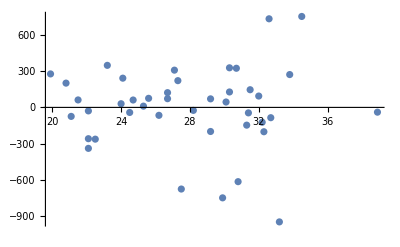

General::stop: 在本次计算中，ListPlot::lpn 的进一步输出将被抑制.

ListPlot::lpn: Table[{data⟦i⟧⟦1⟧,residuals⟦i⟧},{i,1.,n}] 不是由数字或者数对组成的列表.

General::stop: 在本次计算中，Table::iterb 的进一步输出将被抑制.

Table::iterb: 迭代器 {i,1.,n} 没有适当的边界.

Table::iterb: 迭代器 {i,1,n} 没有适当的边界.

FittedModel::argrx: FittedModel[-2149.65+184.553 x] 使用 2 个参数调用；预计有 1 个参数.

```mathematica
ListPlot[Table[{data[[i]][[1]],residuals[[i]]},{i,1,42}],PlotRange->Automatic]
```